```mathematica
(*only run if you have LinKnot*)
SetDirectory["C:\\LinKnot"];
Quiet[<<LinKnots`]
```

```mathematica
(*This is very necessary*)
<<"PDtoConwayData.m"
```

```mathematica
(*This is not really necessary*)
KCD=Import["KCD.csv"];
KCD=Map[{ToExpression[#[[1]]],#[[2]]}&,KCD];
```

```mathematica
isFourPlat[K_]:=StringFreeQ[ConwayNotationNew[K],{"*",".","(",")"}]
```

```mathematica
(*source for finding the Conway notation. This is really just error prevention*)
K=Knot[12,Alternating,1];
messageHandler=If[Last[#],K=NextKnot[K];Continue[]]&;
While[True,
Internal`HandlerBlock[{"Message",messageHandler},
AppendTo[KCD,{K,fFindCon[fPDToPData[K]]}]
];
K = NextKnot[K];If[K[[3]]< 1288,Break[]]
]
Export["KCD12.csv",KCD]
```

```mathematica
(*Use this to compare the diagrams. The first drawing is the original PD code while the second is the PD code after finding it's Conway notation and converting that back into PD code. Initialize KCDdiagrams below. See source below*)
extractKnotFromKCDdiagram[K_]:=Extract[KCDdiagrams,{{Position[KCD,K][[1,1]],2},{Position[KCD,K][[1,1]],3}}]
```

2 3,3,2

(1,1) (1,1,1),(1,1,1),(1,1)

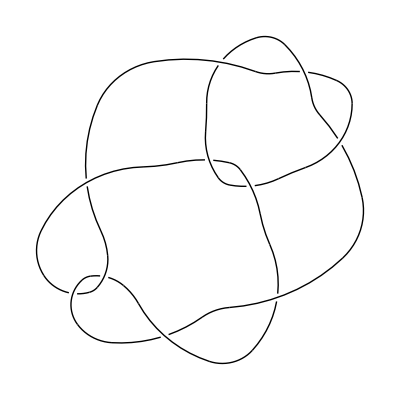
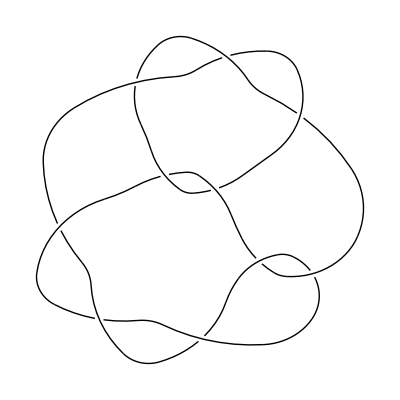

```mathematica
(*Example usage*)
K=Knot[10,54];
ConwayNotationNew[K]
fExpandCon[ConwayNotationNew[K]]
extractKnotFromKCDdiagram[K]
```

```mathematica
(*source for KDCdiagrams*)
KCDdiagrams={};
Do[If[StringQ@ConwayNotationNew[AllKnots[]⟦i⟧],AppendTo[KCDdiagrams,{AllKnots[]⟦i⟧,NewDrawPD[PD[AllKnots[]⟦i⟧],{Gap->0.02}],NewDrawPD[fConwayToPD[ConwayNotationNew[AllKnots[]⟦i⟧]],{Gap->0.02}]}]],{i,1,Length@AllKnots[]}]
```

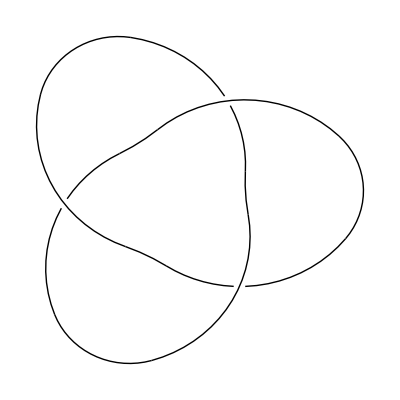
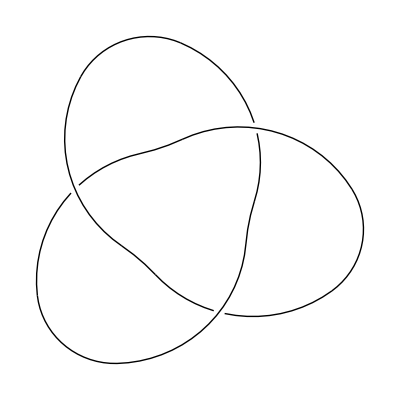
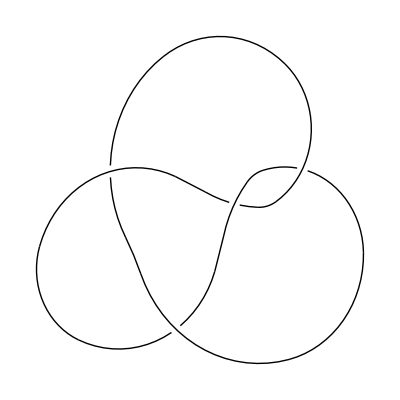
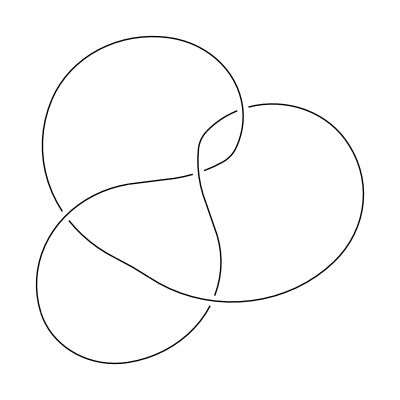
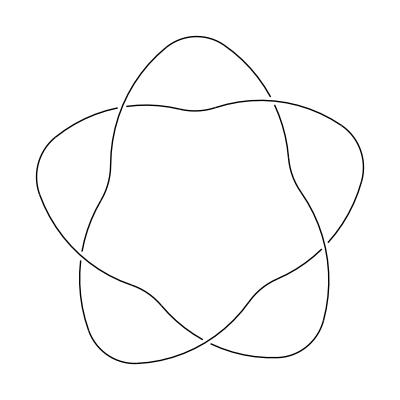
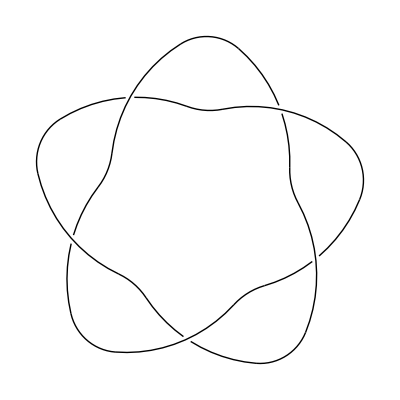
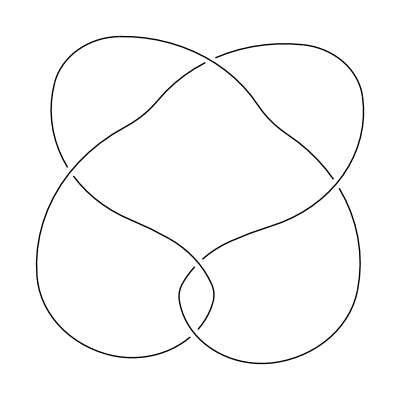
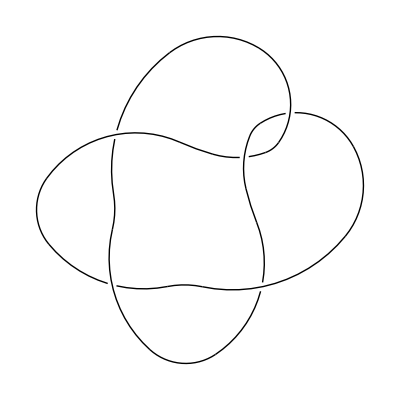
```mathematica
KCDdiagrams={{Knot[3,1],-Graphics-,-Graphics-},{Knot[4,1],-Graphics-,-Graphics-},{Knot[5,1],-Graphics-,-Graphics-},{Knot[5,2],-Graphics-,-Graphics-},{Knot[6,1],-Graphics-,-Graphics-},{Knot[6,2],-Graphics-,-Graphics-},{Knot[6,3],-Graphics-,-Graphics-},{Knot[7,1],-Graphics-,-Graphics-},{Knot[7,2],-Graphics-,-Graphics-},{Knot[7,3],-Graphics-,-Graphics-},{Knot[7,4],-Graphics-,-Graphics-},{Knot[7,5],-Graphics-,-Graphics-},{Knot[7,6],-Graphics-,-Graphics-},{Knot[7,7],-Graphics-,-Graphics-},{Knot[8,1],-Graphics-,-Graphics-},{Knot[8,2],-Graphics-,-Graphics-},{Knot[8,3],-Graphics-,-Graphics-},{Knot[8,4],-Graphics-,-Graphics-},{Knot[8,5],-Graphics-,-Graphics-},{Knot[8,6],-Graphics-,-Graphics-},{Knot[8,7],-Graphics-,-Graphics-},{Knot[8,8],-Graphics-,-Graphics-},{Knot[8,9],-Graphics-,-Graphics-},{Knot[8,10],-Graphics-,-Graphics-},{Knot[8,11],-Graphics-,-Graphics-},{Knot[8,12],-Graphics-,-Graphics-},{Knot[8,13],-Graphics-,-Graphics-},{Knot[8,14],-Graphics-,-Graphics-},{Knot[8,15],-Graphics-,-Graphics-},{Knot[8,16],-Graphics-,-Graphics-},{Knot[8,17],-Graphics-,-Graphics-},{Knot[8,18],-Graphics-,-Graphics-},{Knot[9,1],-Graphics-,-Graphics-},{Knot[9,2],-Graphics-,-Graphics-},{Knot[9,3],-Graphics-,-Graphics-},{Knot[9,4],-Graphics-,-Graphics-},{Knot[9,5],-Graphics-,-Graphics-},{Knot[9,6],-Graphics-,-Graphics-},{Knot[9,7],-Graphics-,-Graphics-},{Knot[9,8],-Graphics-,-Graphics-},{Knot[9,9],-Graphics-,-Graphics-},{Knot[9,10],-Graphics-,-Graphics-},{Knot[9,11],-Graphics-,-Graphics-},{Knot[9,12],-Graphics-,-Graphics-},{Knot[9,13],-Graphics-,-Graphics-},{Knot[9,14],-Graphics-,-Graphics-},{Knot[9,15],-Graphics-,-Graphics-},{Knot[9,16],-Graphics-,-Graphics-},{Knot[9,17],-Graphics-,-Graphics-},{Knot[9,18],-Graphics-,-Graphics-},{Knot[9,19],-Graphics-,-Graphics-},{Knot[9,20],-Graphics-,-Graphics-},{Knot[9,21],-Graphics-,-Graphics-},{Knot[9,22],-Graphics-,-Graphics-},{Knot[9,23],-Graphics-,-Graphics-},{Knot[9,24],-Graphics-,-Graphics-},{Knot[9,25],-Graphics-,-Graphics-},{Knot[9,26],-Graphics-,-Graphics-},{Knot[9,27],-Graphics-,-Graphics-},{Knot[9,28],-Graphics-,-Graphics-},{Knot[9,29],-Graphics-,-Graphics-},{Knot[9,30],-Graphics-,-Graphics-},{Knot[9,31],-Graphics-,-Graphics-},{Knot[9,32],-Graphics-,-Graphics-},{Knot[9,33],-Graphics-,-Graphics-},{Knot[9,34],-Graphics-,-Graphics-},{Knot[9,35],-Graphics-,-Graphics-},{Knot[9,36],-Graphics-,-Graphics-},{Knot[9,37],-Graphics-,-Graphics-},{Knot[9,38],-Graphics-,-Graphics-},{Knot[9,39],-Graphics-,-Graphics-},{Knot[9,40],-Graphics-,-Graphics-},{Knot[9,41],-Graphics-,-Graphics-},{Knot[10,1],-Graphics-,-Graphics-},{Knot[10,2],-Graphics-,-Graphics-},{Knot[10,3],-Graphics-,-Graphics-},{Knot[10,4],-Graphics-,-Graphics-},{Knot[10,5],-Graphics-,-Graphics-},{Knot[10,6],-Graphics-,-Graphics-},{Knot[10,7],-Graphics-,-Graphics-},{Knot[10,8],-Graphics-,-Graphics-},{Knot[10,9],-Graphics-,-Graphics-},{Knot[10,10],-Graphics-,-Graphics-},{Knot[10,11],-Graphics-,-Graphics-},{Knot[10,12],-Graphics-,-Graphics-},{Knot[10,13],-Graphics-,-Graphics-},{Knot[10,14],-Graphics-,-Graphics-},{Knot[10,15],-Graphics-,-Graphics-},{Knot[10,16],-Graphics-,-Graphics-},{Knot[10,17],-Graphics-,-Graphics-},{Knot[10,18],-Graphics-,-Graphics-},{Knot[10,19],-Graphics-,-Graphics-},{Knot[10,20],-Graphics-,-Graphics-},{Knot[10,21],-Graphics-,-Graphics-},{Knot[10,22],-Graphics-,-Graphics-},{Knot[10,23],-Graphics-,-Graphics-},{Knot[10,24],-Graphics-,-Graphics-},{Knot[10,25],-Graphics-,-Graphics-},{Knot[10,26],-Graphics-,-Graphics-},{Knot[10,27],-Graphics-,-Graphics-},{Knot[10,28],-Graphics-,-Graphics-},{Knot[10,29],-Graphics-,-Graphics-},{Knot[10,30],-Graphics-,-Graphics-},{Knot[10,31],-Graphics-,-Graphics-},{Knot[10,32],-Graphics-,-Graphics-},{Knot[10,33],-Graphics-,-Graphics-},{Knot[10,34],-Graphics-,-Graphics-},{Knot[10,35],-Graphics-,-Graphics-},{Knot[10,36],-Graphics-,-Graphics-},{Knot[10,37],-Graphics-,-Graphics-},{Knot[10,38],-Graphics-,-Graphics-},{Knot[10,39],-Graphics-,-Graphics-},{Knot[10,40],-Graphics-,-Graphics-},{Knot[10,41],-Graphics-,-Graphics-},{Knot[10,42],-Graphics-,-Graphics-},{Knot[10,43],-Graphics-,-Graphics-},{Knot[10,44],-Graphics-,-Graphics-},{Knot[10,45],-Graphics-,-Graphics-},{Knot[10,46],-Graphics-,-Graphics-},{Knot[10,47],-Graphics-,-Graphics-},{Knot[10,48],-Graphics-,-Graphics-},{Knot[10,49],-Graphics-,-Graphics-},{Knot[10,50],-Graphics-,-Graphics-},{Knot[10,51],-Graphics-,-Graphics-},{Knot[10,52],-Graphics-,-Graphics-},{Knot[10,53],-Graphics-,-Graphics-},{Knot[10,54],-Graphics-,-Graphics-},{Knot[10,55],-Graphics-,-Graphics-},{Knot[10,56],-Graphics-,-Graphics-},{Knot[10,57],-Graphics-,-Graphics-},{Knot[10,58],-Graphics-,-Graphics-},{Knot[10,59],-Graphics-,-Graphics-},{Knot[10,60],-Graphics-,-Graphics-},{Knot[10,61],-Graphics-,-Graphics-},{Knot[10,62],-Graphics-,-Graphics-},{Knot[10,63],-Graphics-,-Graphics-},{Knot[10,64],-Graphics-,-Graphics-},{Knot[10,65],-Graphics-,-Graphics-},{Knot[10,66],-Graphics-,-Graphics-},{Knot[10,67],-Graphics-,-Graphics-},{Knot[10,68],-Graphics-,-Graphics-},{Knot[10,69],-Graphics-,-Graphics-},{Knot[10,70],-Graphics-,-Graphics-},{Knot[10,71],-Graphics-,-Graphics-},{Knot[10,72],-Graphics-,-Graphics-},{Knot[10,73],-Graphics-,-Graphics-},{Knot[10,74],-Graphics-,-Graphics-},{Knot[10,75],-Graphics-,-Graphics-},{Knot[10,76],-Graphics-,-Graphics-},{Knot[10,77],-Graphics-,-Graphics-},{Knot[10,78],-Graphics-,-Graphics-},{Knot[10,79],-Graphics-,-Graphics-},{Knot[10,80],-Graphics-,-Graphics-},{Knot[10,81],-Graphics-,-Graphics-},{Knot[10,82],-Graphics-,-Graphics-},{Knot[10,83],-Graphics-,-Graphics-},{Knot[10,84],-Graphics-,-Graphics-},{Knot[10,85],-Graphics-,-Graphics-},{Knot[10,86],-Graphics-,-Graphics-},{Knot[10,87],-Graphics-,-Graphics-},{Knot[10,88],-Graphics-,-Graphics-},{Knot[10,89],-Graphics-,-Graphics-},{Knot[10,90],-Graphics-,-Graphics-},{Knot[10,91],-Graphics-,-Graphics-},{Knot[10,92],-Graphics-,-Graphics-},{Knot[10,93],-Graphics-,-Graphics-},{Knot[10,94],-Graphics-,-Graphics-},{Knot[10,95],-Graphics-,-Graphics-},{Knot[10,96],-Graphics-,-Graphics-},{Knot[10,97],-Graphics-,-Graphics-},{Knot[10,98],-Graphics-,-Graphics-},{Knot[10,99],-Graphics-,-Graphics-},{Knot[10,100],-Graphics-,-Graphics-},{Knot[10,101],-Graphics-,-Graphics-},{Knot[10,102],-Graphics-,-Graphics-},{Knot[10,103],-Graphics-,-Graphics-},{Knot[10,104],-Graphics-,-Graphics-},{Knot[10,105],-Graphics-,-Graphics-},{Knot[10,106],-Graphics-,-Graphics-},{Knot[10,107],-Graphics-,-Graphics-},{Knot[10,108],-Graphics-,-Graphics-},{Knot[10,109],-Graphics-,-Graphics-},{Knot[10,110],-Graphics-,-Graphics-},{Knot[10,111],-Graphics-,-Graphics-},{Knot[10,112],-Graphics-,-Graphics-},{Knot[10,113],-Graphics-,-Graphics-},{Knot[10,114],-Graphics-,-Graphics-},{Knot[10,115],-Graphics-,-Graphics-},{Knot[10,116],-Graphics-,-Graphics-},{Knot[10,117],-Graphics-,-Graphics-},{Knot[10,118],-Graphics-,-Graphics-},{Knot[10,119],-Graphics-,-Graphics-},{Knot[10,120],-Graphics-,-Graphics-},{Knot[10,121],-Graphics-,-Graphics-},{Knot[10,122],-Graphics-,-Graphics-},{Knot[10,123],-Graphics-,-Graphics-}};
```